```mathematica
((□_□)_□)_□
```

```mathematica
data1 = {{0,.01},{1,.011},{2,.016},{3,.024},{4,.0372},{4.8,.096},{5,.206},{5.2,.414},{5.4,.786},{5.6,1.26},{5.8,1.91},{6,2.6},{6.2,3.08},{6.4,3.43},{6.6,3.69},{6.8,3.72},{7,3.81},{8,3.82},{9,3.82}};
```

```mathematica
data2 = {{0,.006},{1,.009},{2,.015},{3,.023},{3.8,.04},{4,.055},{4.2,.01},{3.4,.19},{3.6,.32},{3.8,.59},{4,.869},{4.2,1.2},{4.4,1.59},{4.6,1.97},{4.8,2.3},{5,2.7},{5.4,3.03},{5.8,3.43},{6,3.64},{7,3.71}};
```

```mathematica
data3 = {{0,.0003},{1,.0007},{2,.0014},{3,.0845},{4,.419},{5,1.094},{5.2,1.255},{5.6,1.62},{6,1.97},{6.4,2.15},{6.8,2.47},{7,2.78},{7.4,3.15},{8,3.35},{9,3.61}};
```

```mathematica
data4 = {{0,.068},{1,.077},{2,.116},{3,.567},{4,1.16},{4.2,1.35},{4.4,1.59},{4.6,2.19},{4.8,4.07},{5,8.29},{5.2,10.27},{5.4,12},{5.6,13.4},{5.8,15.8},{6,18.9},{6.2,22.7},{6.4,32.9},{6.6,40.5},{6.8,41.8},{7,41.9},{8,41.4},{9,41.6},{10,42.5},{11,42.9},{12, 42.9}};
```

```mathematica
data5={{0,.008},{1,.0607},{2,.259},{3,.467},{4,.756},{5,1.16},{6,2.17},{7,2.9},{8,5.18},{8.2,6.49},{8.4,8.24},{8.6,10.31},{8.8,12.4},{9,14.5},{9.2,16.3},{9.4,17.8},{9.6,18.9},{9.8,19.7},{10,20.4},{11,24.1},{12,27},{13,28.3},{14,29.9},{15,30.6},{16,30.6},{17,30.6},{18,30.6},{19,30.6}};
```

```mathematica
data6 = {{0,.0059},{1,.091},{2,.68},{3,2.30},{4,4.41},{5,6.72},{6,8.91},{7,10.58},{8,11.7},{9,12.7},{10,13.8},{11,15},{12,16.2},{13,17.1},{14,17.8},{15,18.1}};
```

```mathematica
f1 = NonlinearModelFit[data1,P1+.5*P*(Erf[1-w*(x-x1)]),{P,P1,w,x1},x]
```

FittedModel[1.92162-1.89656 Erf[1-1.51913 (-5.13953+x)]]

```mathematica
f2 = NonlinearModelFit[data2,P1+.5*P*(Erf[1-w*(x-x1)]),{P,P1,w,x1},x]
```

FittedModel[1.8017-1.76792 Erf[1-1.26524 (-3.81901+x)]]

```mathematica
f3= NonlinearModelFit[data3,P1+.5*P*(Erf[1-w*(x-x1)]),{P,P1,w,x1},x]
```

FittedModel[1.87292-1.89935 Erf[1-0.415992 (-3.54454+x)]]

```mathematica
f4 = NonlinearModelFit[data4,P1+.5*P*(Erf[1-w*(x-x1)]),{{P,42},{P1,1.5},{w,3.5},{x1,5}},x]
```

FittedModel[22.2219-20.949 Erf[1-1.01383 (-4.98433+x)]]

```mathematica
f5 = NonlinearModelFit[data5,P1+.5*P*(Erf[1-w*(x-x1)]),{{P,30},{P1,1.5},{w,-3.5},{x1,10}},x]
```

FittedModel[15.1777+14.7463 Erf[1+0.448631 (-11.4559+x)]]

```mathematica
f6 = NonlinearModelFit[data6,P1+.5*P*(Erf[1-w*(x-x1)]),{{P,18},{P1,1.5},{w,.5},{x1,10}},x]
```

FittedModel[7.4393-11.0409 Erf[1-0.144026 (1.33165+x)]]

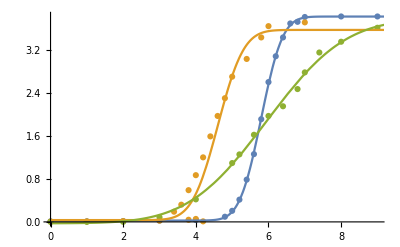

```mathematica
Show[ListPlot[{data1,data2,data3}],Plot[{f1[x],f2[x],f3[x]},{x,0,20}]]
```

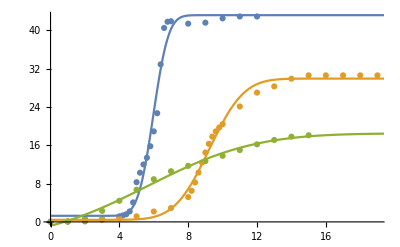

```mathematica
Show[ListPlot[{data4,data5,data6}],Plot[{f4[x],f5[x],f6[x]},{x,0,20}]]
```